```mathematica
Table[With[{g=FindComplement[k,allGraphs5]},
{allGraphs5[k,"colofour"],allGraphs5[g,"colofourrealnull"]}
],{k,allGraphs5AtomKeys}]
```

{{v1x2x3x4x5,n1x2x3x4x5},{v1x2x3x45,n1x2x3x45},{v1x2x35x4,n1x2x35x4},{v1x2x34x5,n1x2x34x5},{v1x2x345,n1x2x345},{v1x25x3x4,n1x25x3x4},{v1x25x34,n1x25x34},{v1x24x3x5,n1x24x3x5},{v1x24x35,n1x24x35},{v1x245x3,n1x245x3},{v1x23x4x5,n1x23x4x5},{v1x23x45,n1x23x45},{v1x235x4,n1x235x4},{v1x234x5,n1x234x5},{v1x2345,n1x2345},{v15x2x3x4,n15x2x3x4},{v15x2x34,n15x2x34},{v15x24x3,n15x24x3},{v15x23x4,n15x23x4},{v15x234,n15x234},{v14x2x3x5,n14x2x3x5},{v14x2x35,n14x2x35},{v14x25x3,n14x25x3},{v14x23x5,n14x23x5},{v14x235,n14x235},{v145x2x3,n145x2x3},{v145x23,n145x23},{v13x2x4x5,n13x2x4x5},{v13x2x45,n13x2x45},{v13x25x4,n13x25x4},{v13x24x5,n13x24x5},{v13x245,n13x245},{v135x2x4,n135x2x4},{v135x24,n135x24},{v134x2x5,n134x2x5},{v134x25,n134x25},{v1345x2,n1345x2},{v12x3x4x5,n12x3x4x5},{v12x3x45,n12x3x45},{v12x35x4,n12x35x4},{v12x34x5,n12x34x5},{v12x345,n12x345},{v125x3x4,n125x3x4},{v125x34,n125x34},{v124x3x5,n124x3x5},{v124x35,n124x35},{v1245x3,n1245x3},{v123x4x5,n123x4x5},{v123x45,n123x45},{v1235x4,n1235x4},{v1234x5,n1234x5},{v12345,n12345}}

```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
Table[With[{g=FindComplement[k,allGraphs5]},
{allGraphs5[k,"colofournull"],ShowGraph5Least[k],allGraphs5[g,"colofourgenerator"],ShowGraph5Least[g]}
],{k,allGraphs5FakeAtomKeys}]
```

{{p1x2x3x4x5,-Graphics-034,g1x2x3x4x5,-Graphics-295240},{p12x3x4x5,-Graphics-1968321,g12x3x4x5,-Graphics-98410},{p12345,-Graphics-295240,g12345,-Graphics-034},{p1234x5,-Graphics-287640,g1234x5,-Graphics-7608},{p1235x4,-Graphics-272460,g1235x4,-Graphics-22788},{p123x4x5,-Graphics-264878,g123x4x5,-Graphics-30371},{p123x45,-Graphics-264885,g123x45,-Graphics-30365},{p1245x3,-Graphics-227080,g1245x3,-Graphics-68168},{p124x3x5,-Graphics-219519,g124x3x5,-Graphics-75731},{p124x35,-Graphics-219545,g124x35,-Graphics-75703},{p125x3x4,-Graphics-204398,g125x3x4,-Graphics-90851},{p125x34,-Graphics-204485,g125x34,-Graphics-90765},{p12x34x5,-Graphics-1969213,g12x34x5,-Graphics-98321},{p12x345,-Graphics-196965,g12x345,-Graphics-98285},{p12x35x4,-Graphics-1968615,g12x35x4,-Graphics-98381},{p12x3x45,-Graphics-1968413,g12x3x45,-Graphics-98401},{p13x2x4x5,-Graphics-656124,g13x2x4x5,-Graphics-229630},{p1345x2,-Graphics-94900,g1345x2,-Graphics-200348},{p134x25,-Graphics-87845,g134x25,-Graphics-207403},{p134x2x5,-Graphics-87579,g134x2x5,-Graphics-207671},{p135x24,-Graphics-73745,g135x24,-Graphics-221503},{p135x2x4,-Graphics-72939,g135x2x4,-Graphics-222311},{p13x24x5,-Graphics-664216,g13x24x5,-Graphics-228820},{p13x245,-Graphics-66705,g13x245,-Graphics-228543},{p13x25x4,-Graphics-658816,g13x25x4,-Graphics-229360},{p13x2x45,-Graphics-656215,g13x2x45,-Graphics-229621},{p14x2x3x5,-Graphics-218724,g14x2x3x5,-Graphics-273370},{p145x23,-Graphics-31605,g145x23,-Graphics-263645},{p145x2x3,-Graphics-29178,g145x2x3,-Graphics-266071},{p14x23x5,-Graphics-243015,g14x23x5,-Graphics-270941},{p14x235,-Graphics-24605,g14x235,-Graphics-270643},{p14x25x3,-Graphics-221416,g14x25x3,-Graphics-273100},{p14x2x35,-Graphics-219016,g14x2x35,-Graphics-273340},{p15x2x3x4,-Graphics-72921,g15x2x3x4,-Graphics-287950},{p15x23x4,-Graphics-97213,g15x23x4,-Graphics-285521},{p15x234,-Graphics-10625,g15x234,-Graphics-284625},{p15x24x3,-Graphics-81015,g15x24x3,-Graphics-287141},{p15x2x34,-Graphics-73813,g15x2x34,-Graphics-287861},{p1x23x4x5,-Graphics-24321,g1x23x4x5,-Graphics-292810},{p1x2345,-Graphics-3640,g1x2345,-Graphics-291608},{p1x234x5,-Graphics-3338,g1x234x5,-Graphics-291911},{p1x235x4,-Graphics-2739,g1x235x4,-Graphics-292511},{p1x23x45,-Graphics-24413,g1x23x45,-Graphics-292801},{p1x24x3x5,-Graphics-8124,g1x24x3x5,-Graphics-294430},{p1x245x3,-Graphics-1099,g1x245x3,-Graphics-294151},{p1x24x35,-Graphics-8416,g1x24x35,-Graphics-294400},{p1x25x3x4,-Graphics-2724,g1x25x3x4,-Graphics-294970},{p1x25x34,-Graphics-3615,g1x25x34,-Graphics-294881},{p1x2x34x5,-Graphics-921,g1x2x34x5,-Graphics-295150},{p1x2x345,-Graphics-138,g1x2x345,-Graphics-295111},{p1x2x35x4,-Graphics-324,g1x2x35x4,-Graphics-295210},{p1x2x3x45,-Graphics-121,g1x2x3x45,-Graphics-295230}}

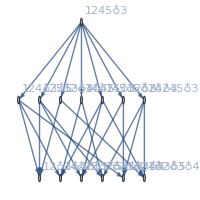
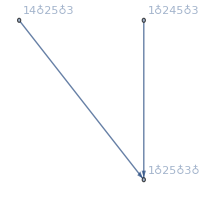
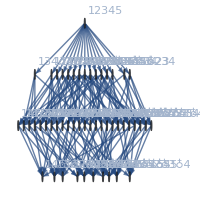
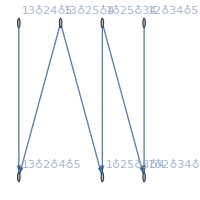
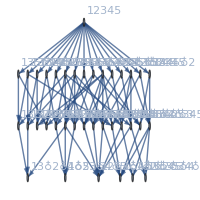
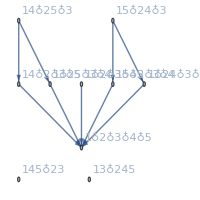
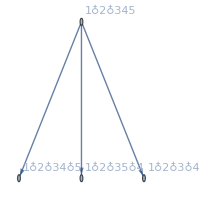
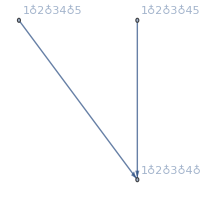
-Graphics-272282 | -Graphics- | -Graphics-22966 | -Graphics-
-Graphics-31633 | -Graphics- | -Graphics-263615 | -Graphics-
-Graphics-1969510 | -Graphics- | -Graphics-98292 | -Graphics-
-Graphics-295140 | -Graphics- | -Graphics-1013 | -Graphics-
-Graphics-552513 | -Graphics- | -Graphics-537342 | -Graphics-
-Graphics-290381 | -Graphics- | -Graphics-12158 | -Graphics-
-Graphics-66705 | -Graphics- | -Graphics-228543 | -Graphics-
-Graphics-30342 | -Graphics- | -Graphics-264906 | -Graphics-
-Graphics-1992613 | -Graphics- | -Graphics-95980 | -Graphics-
-Graphics-492041 | -Graphics- | -Graphics-393699 | -Graphics-

```mathematica
TableForm[Table[With[{g=FindComplement[k,allGraphs5]},
{ShowGraph5Least[k],
FormulaGraphReverse[ListofVars[allGraphs5[g,"colofournull"]]],
ShowGraph5Least[g],
FormulaGraphReverse[ListofVars[allGraphs5[k,"colofourgenerator"]]]}
],{k,RandomSample[Keys[allGraphs5],10]}]]
```

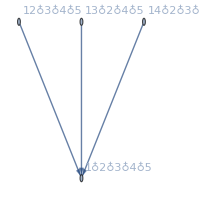

```mathematica
FormulaGraphReverse[ListofVars[g12x3x4x5+g13x2x4x5+g14x2x3x5-2 g1x2x3x4x5]]
```

```mathematica
FormulaGraphReverse[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel[ SetsToSymbol[s]],Pi/4],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding",ImageSize->{Max[15*Length[vert],50],Automatic}]
]
```

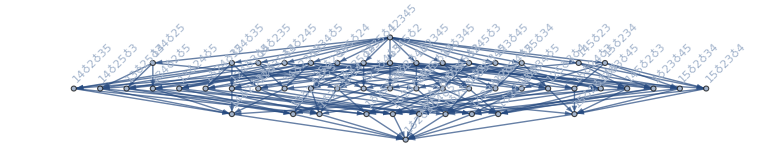
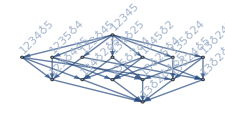
-Graphics-295240
-Graphics-034 | -Graphics-comp fullp1x2x3x4x5
-Graphics-gr nullg1x2x3x4x5
-Graphics-360850
-Graphics-1312210 | -Graphics-comp full-p13x2x4x5+p1x2x3x4x5
-Graphics-gr nullg13x2x4x5-g1x2x3x4x5
-Graphics-361660
-Graphics-132842 | -Graphics-comp fullp13x24x5-p13x2x4x5-p1x24x3x5+p1x2x3x4x5
-Graphics-gr nullg13x24x5-g13x2x4x5-g1x24x3x5+g1x2x3x4x5
-Graphics-298881
-Graphics-7282 | -Graphics-comp full1/6 (-p1x2345+p1x234x5+p1x235x4+p1x23x45-2 p1x23x4x5+p1x245x3+p1x24x35-2 p1x24x3x5+p1x25x34-2 p1x25x3x4+p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45+6 p1x2x3x4x5)
-Graphics-gr nullg1x2345-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5-g1x245x3-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5
-Graphics-034
-Graphics-295240 | -Graphics-comp fullp12345
-Graphics-gr nullg12345

```mathematica
TableForm[Table[With[{g=FindComplement[k,allGraphs5]},
{{ShowGraph5Least[k],ShowGraph5Least[g]},
Column[
{
Row[{Labeled[FormulaGraphReverse[ListofVars[allGraphs5[g,"colofour"]]],"comp full"],
TextCell[allGraphs5[g,"colofournull"],CellSize->{400,200}]}],
Row [{Labeled[FormulaGraphReverse[ListofVars[allGraphs5[k,"colofourrealnull"]]],"gr null"],
TextCell[allGraphs5[k,"colofourgenerator"],CellSize->{400,200}]}]
}
]
}]
,{k,{K5Key,quad1Key,alfa1Key,29888,0}}]]
```

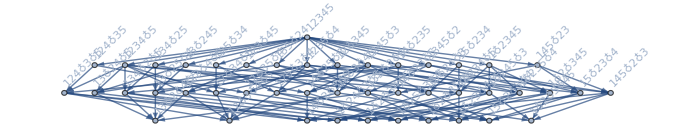
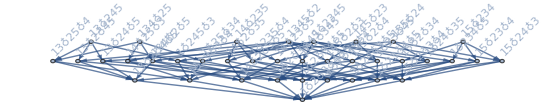
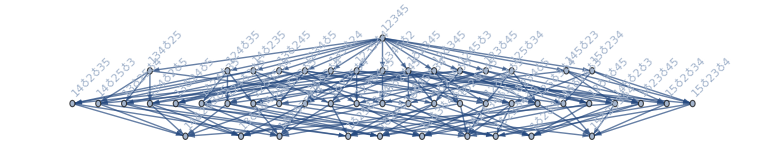
-Graphics-034
-Graphics-295240 | -Graphics-fakep12345
-Graphics-geng12345
-Graphics-1968321
-Graphics-98410 | -Graphics-fake1/12 (9 p12345-p1234x5-p1235x4-3 p123x45+2 p123x4x5-p1245x3-3 p124x35+2 p124x3x5-3 p125x34+2 p125x3x4-9 p12x345+4 p12x34x5+4 p12x35x4+4 p12x3x45-6 p12x3x4x5+3 p1345x2+3 p134x25-2 p134x2x5+3 p135x24-2 p135x2x4+3 p13x245-2 p13x24x5-2 p13x25x4+2 p13x2x4x5+3 p145x23-2 p145x2x3+3 p14x235-2 p14x23x5-2 p14x25x3+2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x24x3+2 p15x2x3x4+3 p1x2345-2 p1x234x5-2 p1x235x4+2 p1x23x4x5-2 p1x245x3+2 p1x24x3x5+2 p1x25x3x4+6 p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45)
-Graphics-geng1345x2+g134x25-g134x2x5+g135x24-g135x2x4+g13x245-g13x24x5-g13x25x4-g13x2x45+2 g13x2x4x5+g145x23-g145x2x3+g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5+g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4+g1x2345-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5-g1x245x3-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5
-Graphics-295240
-Graphics-034 | -Graphics-fakep1x2x3x4x5
-Graphics-geng1x2x3x4x5
-Graphics-287640
-Graphics-7608 | -Graphics-fake1/24 (p12345-p1234x5+3 p1235x4-p123x45-2 p123x4x5+3 p1245x3-p124x35-2 p124x3x5-p125x34+6 p125x3x4-p12x345+2 p12x34x5-2 p12x35x4-2 p12x3x45-2 p12x3x4x5+3 p1345x2-p134x25-2 p134x2x5-p135x24+6 p135x2x4-p13x245+2 p13x24x5-2 p13x25x4-2 p13x2x45-2 p13x2x4x5-p145x23+6 p145x2x3-p14x235+2 p14x23x5-2 p14x25x3-2 p14x2x35-2 p14x2x3x5-p15x234-2 p15x23x4-2 p15x24x3-2 p15x2x34+6 p15x2x3x4+3 p1x2345-2 p1x234x5+6 p1x235x4-2 p1x23x45-2 p1x23x4x5+6 p1x245x3-2 p1x24x35-2 p1x24x3x5-2 p1x25x34+6 p1x25x3x4+6 p1x2x345-2 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45)
-Graphics-geng15x2x3x4+g1x25x3x4+g1x2x35x4+g1x2x3x45-3 g1x2x3x4x5
-Graphics-272460
-Graphics-22788 | -Graphics-fake1/24 (p12345+3 p1234x5-p1235x4-p123x45-2 p123x4x5+3 p1245x3-p124x35+6 p124x3x5-p125x34-2 p125x3x4-p12x345-2 p12x34x5+2 p12x35x4-2 p12x3x45-2 p12x3x4x5+3 p1345x2-p134x25+6 p134x2x5-p135x24-2 p135x2x4-p13x245-2 p13x24x5+2 p13x25x4-2 p13x2x45-2 p13x2x4x5-p145x23+6 p145x2x3-p14x235-2 p14x23x5-2 p14x25x3-2 p14x2x35+6 p14x2x3x5-p15x234+2 p15x23x4-2 p15x24x3-2 p15x2x34-2 p15x2x3x4+3 p1x2345+6 p1x234x5-2 p1x235x4-2 p1x23x45-2 p1x23x4x5+6 p1x245x3-2 p1x24x35+6 p1x24x3x5-2 p1x25x34-2 p1x25x3x4+6 p1x2x345+6 p1x2x34x5-2 p1x2x35x4+6 p1x2x3x45)
-Graphics-geng14x2x3x5+g1x24x3x5+g1x2x34x5+g1x2x3x45-3 g1x2x3x4x5

```mathematica
TableForm[Table[With[{g=FindComplement[k,allGraphs5]},
{{ShowGraph5Least[k],ShowGraph5Least[g]},
Column[
{
Row[{Labeled[FormulaGraphReverse[ListofVars[allGraphs5[g,"colofournull"]]],"fake"],
TextCell[allGraphs5[g,"colofournull"],CellSize->{400,Automatic}]}],
Row [{Labeled[FormulaGraphReverse[ListofVars[allGraphs5[k,"colofourgenerator"]]],"gen"],
TextCell[allGraphs5[k,"colofourgenerator"],CellSize->{400,Automatic}]}]
}
]
}]
,{k,Take[allGraphs5FakeAtomKeys,5]}]]
```

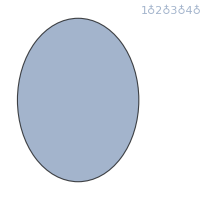
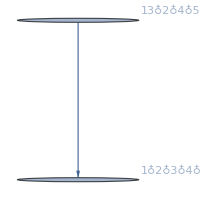
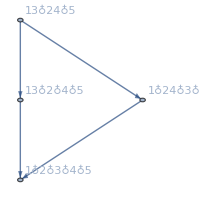
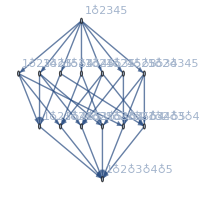
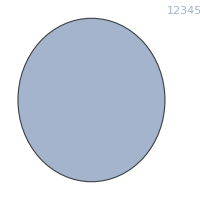
-Graphics-295240 | -Graphics-fakep1x2x3x4x5
-Graphics-geng1x2x3x4x5
-Graphics-360850 | -Graphics-fake-p13x2x4x5+p1x2x3x4x5
-Graphics-geng13x2x4x5-g1x2x3x4x5
-Graphics-361660 | -Graphics-fakep13x24x5-p13x2x4x5-p1x24x3x5+p1x2x3x4x5
-Graphics-geng13x24x5-g13x2x4x5-g1x24x3x5+g1x2x3x4x5
-Graphics-298881 | -Graphics-fake1/6 (-p1x2345+p1x234x5+p1x235x4+p1x23x45-2 p1x23x4x5+p1x245x3+p1x24x35-2 p1x24x3x5+p1x25x34-2 p1x25x3x4+p1x2x345-2 p1x2x34x5-2 p1x2x35x4-2 p1x2x3x45+6 p1x2x3x4x5)
-Graphics-geng1x2345-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5-g1x245x3-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5
-Graphics-034 | -Graphics-fakep12345
-Graphics-geng12345

```mathematica
TableForm[Table[With[{g=FindComplement[k,allGraphs5]},
{ShowGraph5Least[k],
Column[
{
Row[{Labeled[FormulaGraphReverse[ListofVars[allGraphs5[g,"colofournull"]]],"fake"],
allGraphs5[g,"colofournull"]}],
Row [{Labeled[FormulaGraphReverse[ListofVars[allGraphs5[k,"colofourgenerator"]]],"gen"],
allGraphs5[k,"colofourgenerator"]}]
}
]
}]
,{k,{K5Key,quad1Key,alfa1Key,29888,0}}]]
```